# Impementation of the Koshland-Némethy-Filmer Model of Allostery in Mathematica.

## David M. Morgan, Ph.D.

Establish the root directory beneath which files for the KNF implementation occur. 
Establish the directory in which KNF implementation files occur.
Navigate to that directory.

```mathematica
basedirectory = Input[
"Write a properly formatted path to the base directory: ",
"D:\\papers and presentations\\MWC KNF Post IMS"
];

knffuncdir = "IMS2012 KNF functions";

dirarg = basedirectory <> "\\" <> knffuncdir;

SetDirectory[
dirarg
]
```

D:\papers and presentations\MWC KNF Post IMS\IMS2012 KNF functions

```mathematica
(* KNFSolve *)
<<"KNFSolvevH.m"
```

Function KNFSolvevH

Usage:

KNFSolvevH[
{kd1_, kd2_, kd3_, kd4_, PO2_, totalHb_}
]

in which:

	kd1		dissociation constant for the first oxygen binding event
	kd2		dissociation constant for the second oxygen binding event
	kd3		dissociation constant for the third oxygen binding event
	kd4		dissociation constant for the fourth oxygen binding event
	PO2		partial pressure of oxygen above solution, torr
	totalHb	total amount of hemoglobin in the system, molar

Returns:

{
O2, T4RO20, T3RO21, T2RO22, T1RO23, T0RO24
}

```mathematica
KNFSolvevH[
{.0001, .00001, .000001, .000000110, 10, 1}
]
```

{{0.0000171053,0.00127432,0.000217976,0.000372854,0.00637776,0.991757}}

```mathematica
<<"D:\\papers and presentations\\MWC KNF\\IMS2012 Presentation\\IMS\\things I need in London\\KNF\\KNFGenerateDataSetvH.m"
```

Function KNFGenerateDataSetvH

Usage:

KNFGenerateDataSetvH[
{kd1_, kd2_, kd3_, kd4_, totalHb_, minPO2_, maxPO2_, numPoints_}
]

in which:
	kd1		dissociation constant for the first oxygen binding event
	kd2		dissociation constant for the second oxygen binding event
	kd3		dissociation constant for the third oxygen binding event
	kd4		dissociation constant for the fourth oxygen binding event
	totalHb	total amount of hemoglobin in the system (molar)
	minPO2	 minimum partial pressure of oxygen above solution (torr)
	maxPO2	 maximum partial pressure of oxygen above solution (torr)
	numPoints  the number of points for which to compute solutions

Returns:

A list of length numPoints the elements of which are

{
PO2, Y, O2, T4RO20, T3RO21, T2RO22, T1RO23, T0RO24
}

in which:
	PO2	   partial pressure of oxygen above solution (torr)
	Y		 fraction of available sites which are occupied by oxygen
	O2	    concentration (molar) of oxygen in solution 
	T4RO20	concentration (molar) of the species to which no oxygen is bound
	T4RO21	concentration (molar) of the singly oxygen bound species
	T4RO22	concentration (molar) of the doubly oxygen bound species
	T4RO23	concentration (molar) of the triply oxygen bound species
	T4RO24	concentration (molar) of the quadruply oxygen bound species

```mathematica
kd1 = .0001;
kd2 = .00005;
kd3 = .00001;
kd4 = .000005;

totalHb = .01;
minPO2 = .001;
maxPO2 = 65;
numPoints = 50;

arguments = {
kd1,kd2,kd3,kd4,totalHb, minPO2, maxPO2, numPoints
};

knfsolutionset = KNFGenerateDataSetvH[
arguments
];
```

```mathematica
<<"D:\\papers and presentations\\MWC KNF\\IMS2012 Presentation\\IMS\\things I need in London\\KNF\\KNFPlot.m"
```

Function KNFPlot

Usage:  

KNFPlot[
YString_, XString_, KNFDataSet_, ColourArgument_
]

in which each of 
	YString and
	XString
may take on any of the following values:
	PO2, Y, O2
	T4RO20, T3RO21, T2RO22, T1RO23, T0RO24
	fT4RO20, fT3RO21, fT2RO22, fT1RO23, fT0RO24

	KNFDataSet		is the name of a dataset generated by
					  KNFGenerateDataSet
	ColourArgument	is the desired colour for the plot.

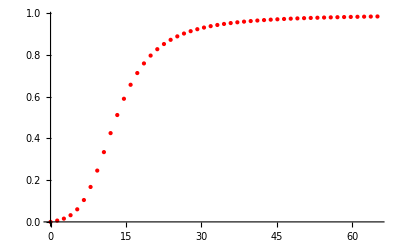

```mathematica
YvsPO2plot = KNFPlot[
"Y", "PO2", knfsolutionset, Red
]
```

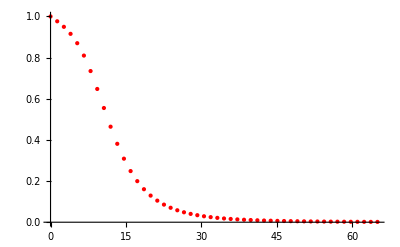
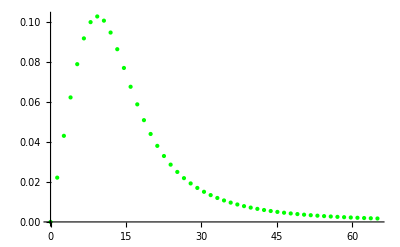
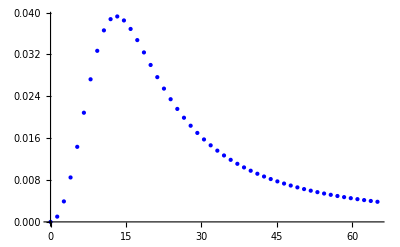
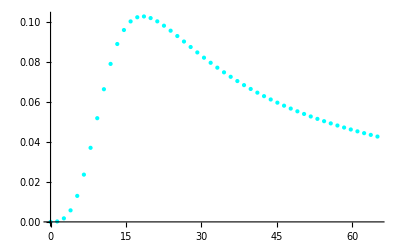
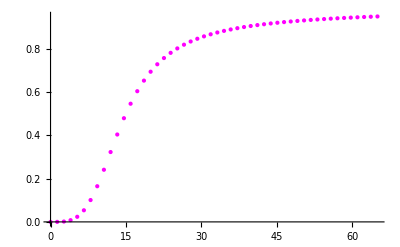

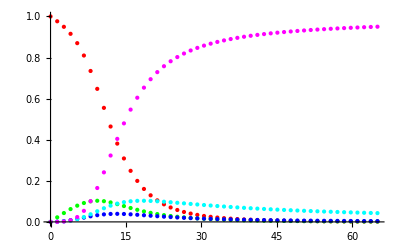

```mathematica
SpeciesStringTable = {
"fT4RO20", "fT3RO21", "fT2RO22", "fT1RO23", "fT0RO24"
};

ColourList = {
Red, Green, Blue, Cyan, Magenta
};

KNFSpeciesPlots = Table[
KNFPlot[
SpeciesStringTable[[i]],
"PO2", 
knfsolutionset,
ColourList[[i]]
],
{i, Length[SpeciesStringTable]}
]

Show[
Table[
KNFSpeciesPlots[[i]],
{i, Length[KNFSpeciesPlots]}
]
]
```

How does the KNF model vary with the dissociation constants?

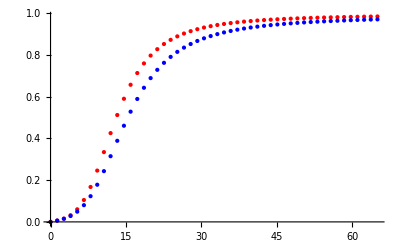

```mathematica
kd1 = .0001 ;
kd2 = .00005 ;
kd3 = .00001 ;
kd4 = 2 .000005;

totalHb = .01;
minPO2 = .001;
maxPO2 = 65;
numPoints = 50;

arguments = {
kd1,kd2,kd3,kd4,totalHb, minPO2, maxPO2, numPoints
};

knfsolutionset = KNFGenerateDataSetvH[
arguments
];

YvsPO2smallerkds = KNFPlot[
"Y", "PO2", knfsolutionset, Blue
];

Show[
YvsPO2plot,
YvsPO2smallerkds
]
```